# Exploration of Tanzania (Nyakatoke) village risk sharing network structure

Villagers in Nyakatoke were asked to list people who they could ask for assistance, or who could ask them for assistance, when faced with financial difficulties  In the reported data, sometimes both households list the other, and sometimes only one lists the other.  We create three networks from this graph:

An undirected graph where we assume that links are underreported.  If either Household says there is a link with the other, we insert the corresponding edge in the graph

An undirected graph where we assume that links are overreported.  We require both households to report the link before we insert the corresponding edge in the graph

A directed graph where we assume that a household listing another household means they wish (desire) for a link between the households exist.  No actual link may exist.  Since thse desires might not be symmteric, the graph is directed.

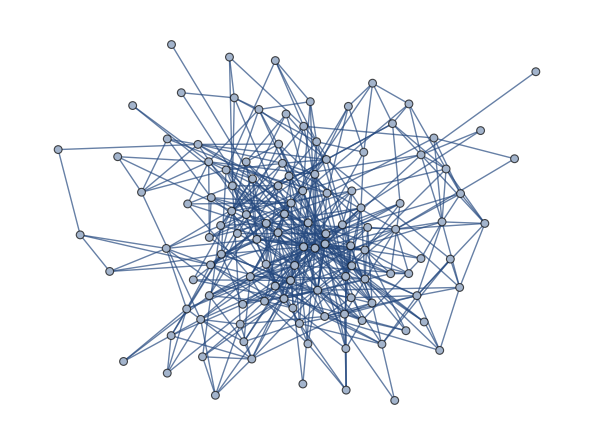

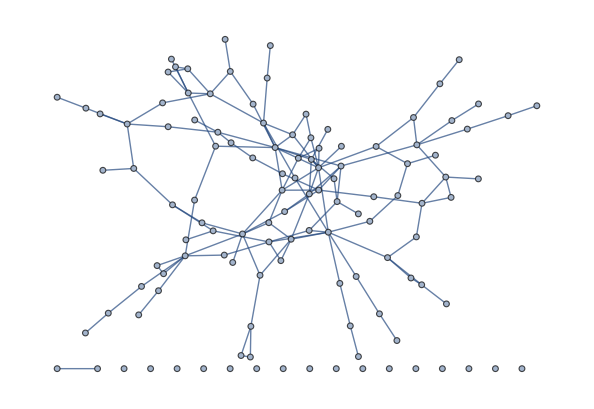

-Graphics-

```mathematica
underReportingGraph = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"data","underreporting_model.graphml"}]]
overReportingGraph = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"data","overreporting_model.graphml"}]]
desireToLinkGraph = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "data", "desire_to_link_model.graphml"}]]
```

## Basic Statistics

```mathematica
sizeUnderReporting = EdgeCount[underReportingGraph]
sizeOverReporting = EdgeCount[overReportingGraph]
sizeDesireToLink = EdgeCount[desireToLinkGraph]
```

490

140

630

```mathematica
orderUnderReporting = VertexCount[underReportingGraph]
orderOverReporting = VertexCount[overReportingGraph]
orderDesireToLink = VertexCount[desireToLinkGraph]
```

119

119

119

```mathematica
clusteringCoefficientUnderReporting = GlobalClusteringCoefficient[underReportingGraph]
clusteringCoefficientOverReporting = GlobalClusteringCoefficient[overReportingGraph]
clusteringCoefficientDesireToLink = GlobalClusteringCoefficient[desireToLinkGraph]
clusteringCoefficientDesireToLinkAsUndirected = GlobalClusteringCoefficient[UndirectedGraph[desireToLinkGraph]]
```

189/1003

33/410

129/1274

189/1003

```mathematica
avgClusteringUnderReporting = MeanClusteringCoefficient[underReportingGraph]
avgClusteringOverReporting = MeanClusteringCoefficient[overReportingGraph]
avgClusteringDesireToLink = MeanClusteringCoefficient[desireToLinkGraph]
avgClusteringDesireToLinkAsUndirected = MeanClusteringCoefficient[UndirectedGraph[desireToLinkGraph]]
```

102131927129/438927785296

2299/29988

213243970651810993820440133648/1867895371408044552144806460225

102131927129/438927785296

```mathematica
dUnderReporting = GraphDiameter[underReportingGraph]
dOverReporting = GraphDiameter[overReportingGraph]
dDesireToLink = GraphDiameter[desireToLinkGraph]
```

5

∞

∞

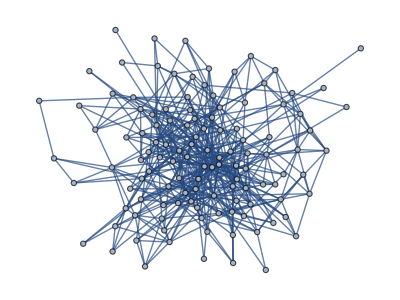

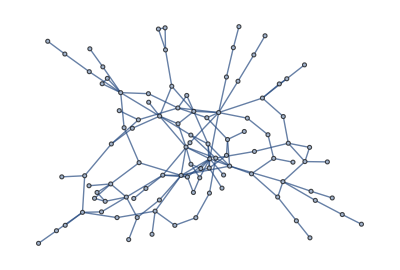

-Graphics-

```mathematica
giantComponentUnderReporting = ConnectedComponents[underReportingGraph]//First // Subgraph[underReportingGraph, #]&
giantComponentOverReporting = ConnectedComponents[overReportingGraph] // First // Subgraph[overReportingGraph, #] &
giantComponentDesireToLink = WeaklyConnectedComponents[desireToLinkGraph] // First // Subgraph[desireToLinkGraph, #]&
```

```mathematica
aplUnderReporting = MeanGraphDistance[giantComponentUnderReporting]
aplOverReporting = MeanGraphDistance[giantComponentOverReporting]
aplDesireToLink = MeanGraphDistance[giantComponentDesireToLink]
```

17994/7021

12109/2525

∞

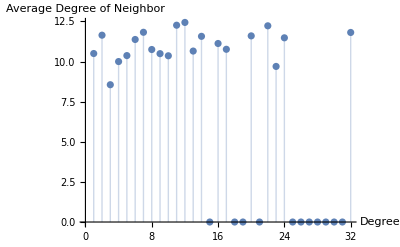

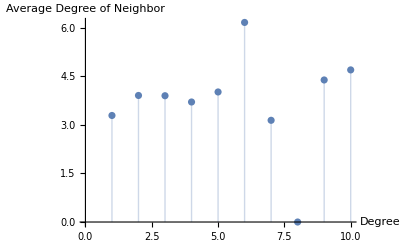

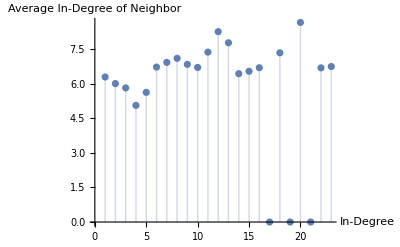

0.0332259

0.0857553

0.0672929

```mathematica
ListPlot[Rest[MeanDegreeConnectivity[underReportingGraph]], Filling->Axis, AxesLabel->{"Degree", "Average Degree of Neighbor"}]
ListPlot[Rest[MeanDegreeConnectivity[overReportingGraph]], Filling->Axis, AxesLabel->{"Degree", "Average Degree of Neighbor"}]
ListPlot[Rest[MeanDegreeConnectivity[desireToLinkGraph, "In"]], Filling->Axis, AxesLabel->{"In-Degree", "Average In-Degree of Neighbor"}]
N[GraphAssortativity[underReportingGraph]]
N[GraphAssortativity[overReportingGraph]]
N[GraphAssortativity[desireToLinkGraph]]
```

```mathematica
N[10223/(8 √360610651)]
```

0.0672929

## Simulations

```mathematica
(*underReportingER = RandomGraph[UniformGraphDistribution[orderUnderReporting, sizeUnderReporting], 100000];
overReportingER = RandomGraph[UniformGraphDistribution[orderOverReporting, sizeOverReporting], 100000];
desireToLinkER= RandomGraph[UniformGraphDistribution[orderDesireToLink, sizeDesireToLink], 100000, DirectedEdges->True]; *)
```

```mathematica
(*underReportingConfig = RandomGraph[DegreeGraphDistribution[VertexDegree[underReportingGraph]], 100000];
overReportingConfig = RandomGraph[DegreeGraphDistribution[VertexDegree[overReportingGraph]], 100000];
desireToLinkConfig = RandomGraph[DegreeGraphDistribution[VertexInDegree[desireToLinkGraph]], 100000, DirectedEdges->True];*)
```

### Clustering

#### Erdos-Renyi

```mathematica
(*erSimUnderReportingClusteringCoefficientMean = Mean[Map[GlobalClusteringCoefficient, underReportingER]];
erSimOverReportingClusteringCoefficientMean = Mean[Map[GlobalClusteringCoefficient, overReportingER]];
erSimDesireToLinkClusteringCoefficientMean = Mean[Map[GlobalClusteringCoefficient, desireToLinkER]];*)
```

```mathematica
(*erSimUnderReportingClusteringCoefficientSD = StandardDeviation[Map[GlobalClusteringCoefficient, underReportingER]];
erSimOverReportingClusteringCoefficientSD = StandardDeviation[Map[GlobalClusteringCoefficient, overReportingER]];
erSimDesireToLinkClusteringCoefficientSD = StandardDeviation[Map[GlobalClusteringCoefficient, desireToLinkER]];*)
```

#### Configuration

```mathematica
(*configSimUnderReportingClusteringCoefficientMean = Mean[Map[GlobalClusteringCoefficient, underReportingConfig]];
configSimOverReportingClusteringCoefficientMean =  Mean[Map[GlobalClusteringCoefficient, overReportingConfig]];
configSimDesireToLinkClusteringCoefficientMean = Mean[Map[GlobalClusteringCoefficient, desireToLinkConfig]];*)
```

```mathematica
(*configSimUnderReportingClusteringCoefficientSD = StandardDeviation[Map[GlobalClusteringCoefficient, underReportingConfig]];
configSimOverReportingClusteringCoefficientSD =  StandardDeviation[Map[GlobalClusteringCoefficient, overReportingConfig]];
configSimDesireToLinkClusteringCoefficientSD = StandardDeviation[Map[GlobalClusteringCoefficient, desireToLinkConfig]];*)
```

### Diameter

#### Erdos-Renyi

```mathematica
(*erSimUnderReportingDiameterMean = Mean[Map[GraphDiameter, underReportingER]];
erSimOverReportingDiameterMean = Mean[Map[GraphDiameter, underReportingER]];
erSimDesireToLinkDiameterMean = Mean[ap[GraphDiameter, underReportingER]];*)
```

```mathematica
(*erSimUnderReportingDiameterSD = StandardDeviation[Map[GraphDiameter, underReportingER]];
erSimOverReprtingDiameterSD = StandardDeviation[Map[GraphDiameter, underReportingER]];
erSimDesireToLinkDiameterSD = StandardDeviation[Map[GraphDiameter, underReportingER]];*)
```

#### Configuration

```mathematica
(*configSimUnderReportingDiameterMean= Map[GraphDiameter, underReportingConfig]//Mean;
configSimOverReportingDiameterMean = Map[GraphDiameter, overReportingConfig]//Mean;
configSimesireToLinkDiameterMean = Map[GraphDiameter, desireToLinkConfig]//Mean;*)
```

```mathematica
(*configSimUnderReportingDiameterSD = Map[GraphDiameter, underReportingConfig] // StandardDeviation;
configSimOverReprtingDiameterSD = Map[GraphDiameter, overReportingConfig] // StandardDeviation;
configSimDesireToLinkDiameterSD = Map[GraphDiameter, desireToLinkConfig] // StandardDeviation;*)
```

### Average Path Length

#### Erdos-Renyi

```mathematica
(*erSimUnderReportingAplMean = Map[MeanGraphDistance, underReportingER]//Mean;
erSimOverReportingAplMean = Map[MeanGraphDistance, overReportingER]//Mean;
erSimDesireToLinkAplMean = Map[MeanGraphDistance, desireToLinkER]//Mean;
```

```mathematica
(*erSimUnderReportingAplSD = Map[MeanGraphDistance, underReportingER]//StandardDeviation;
erSimOverReprtingAplSD = Map[MeanGraphDistance, overReportingConfig]//StandardDeviation;
erSimDesireToLinkAplSD = Map[MeanGraphDistance, desireToLinkER]//StandardDeviation;*)
```

#### Configuration

```mathematica
(*configSimUnderReportingAplMean = Map[MeanGraphDistance, underReportingConfig]//Mean;
configSimOverReportingAplMean = Map[MeanGraphDistance, overReportingConfig]//Mean;
configSimesireToLinkAplMean = Map[MeanGraphDistance, desireToLinkConfig]//Mean;*)
```

```mathematica
(*configSimUnderReportingAplSD = Map[MeanGraphDistance, underReportingConfig]//StandardDeviation;
configSimOverReprtingAplSD = Map[MeanGraphDistance, overReportingConfig]//StandardDeviation;
configSimDesireToLinkAplSD = Map[MeanGraphDistance, desireToLinkConfig]//StandardDeviation;*)
```